# Figure out what the fuck to do with polylogs

```mathematica
X1[mh_,m1_,m2_]:= (2mh^2)/(-m1^2+mh^2+m2^2-Sqrt[(-m1^2+m2^2+mh^2)^2-4m2^2 mh^2])
X2[mh_,m1_,m2_]:= (2mh^2)/(-m1^2+mh^2+m2^2+Sqrt[(-m1^2+m2^2+mh^2)^2-4m2^2 mh^2])
X3[mh_,m1_,m2_]:= (2mh^2)/(-m2^2+mh^2+m1^2-Sqrt[(-m2^2+m1^2+mh^2)^2-4m1^2 mh^2])
X4[mh_,m1_,m2_]:= (2mh^2)/(-m2^2+mh^2+m1^2+Sqrt[(-m2^2+m1^2+mh^2)^2-4m1^2 mh^2])
Y1[mh_,m1_,m2_]:= (mh^2 - m1^2+m2^2)/m2^2
Y2[mh_,m1_,m2_]:= (mh^2 - m2^2+m1^2)/m1^2
```

```mathematica
X1[x,y,z]
X2[x,y,z]
X3[x,y,z];
X4[x,y,z];
Y1[x,y,z];
Y2[x,y,z];
```

(2 x^2)/(x^2-y^2+z^2-√(-4 x^2 z^2+(x^2-y^2+z^2)^2))

(2 x^2)/(x^2-y^2+z^2+√(-4 x^2 z^2+(x^2-y^2+z^2)^2))

```mathematica
X1[125,150,200]
```

31250/(33125-1875 ⅈ √399)

```mathematica
Abs[%]
```

5/8

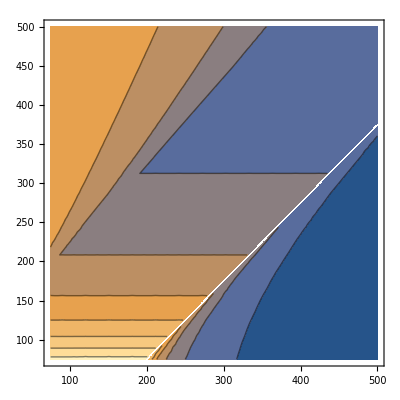

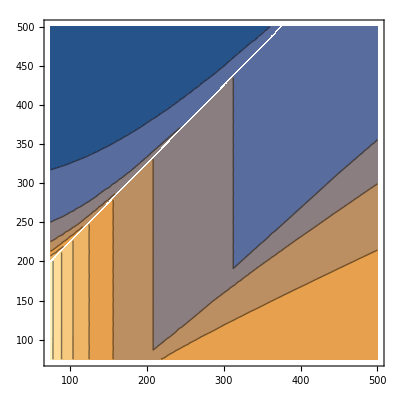

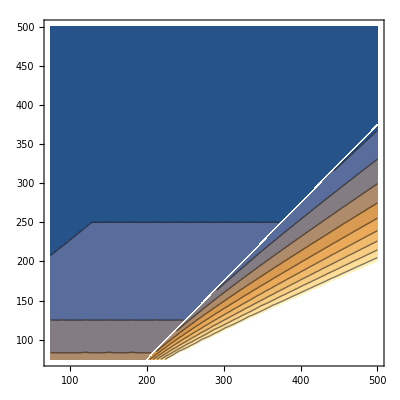

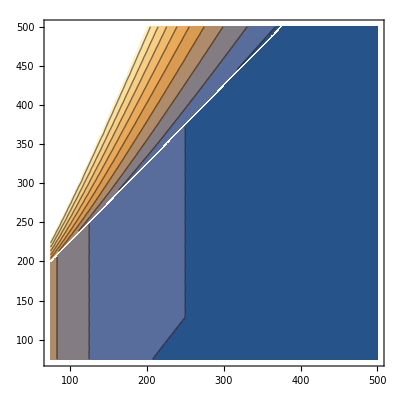

```mathematica
ContourPlot[Abs[X1[125,x,y]],{x,75,500},{y,75,500}]
ContourPlot[Abs[X3[125,x,y]],{x,75,500},{y,75,500}]
ContourPlot[Abs[X2[125,x,y]],{x,75,500},{y,75,500}]
ContourPlot[Abs[X4[125,x,y]],{x,75,500},{y,75,500}]
```

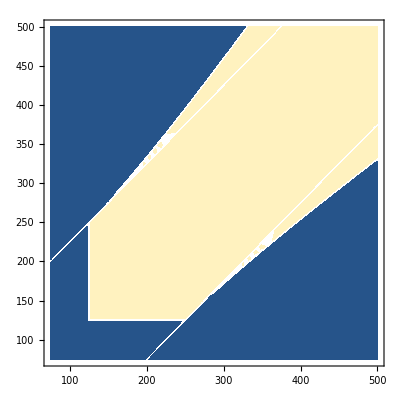

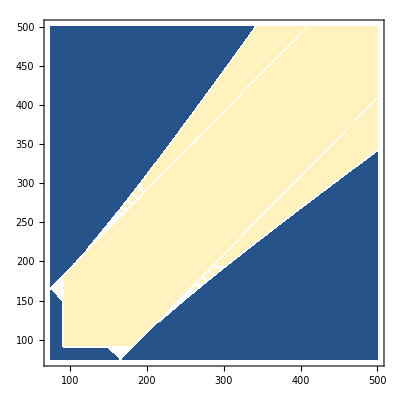

```mathematica
ContourPlot[If[Abs[X1[125,x,y]]<=1&&Abs[X2[125,x,y]]<=1&&Abs[X3[125,x,y]]<=1&&Abs[X4[125,x,y]]<=1,1,0],{x,75,500},{y,75,500}]
ContourPlot[If[Abs[X1[91.2,x,y]]<=1&&Abs[X2[91.2,x,y]]<=1&&Abs[X3[91.2,x,y]]<=1&&Abs[X4[91.2,x,y]]<=1,1,0],{x,75,500},{y,75,500}]
```

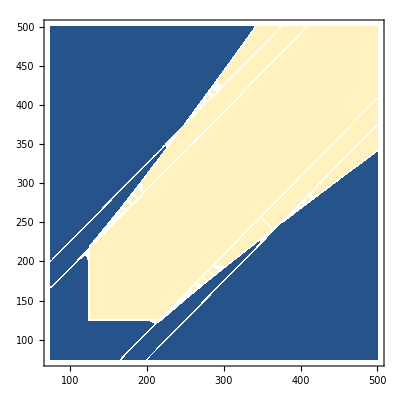

```mathematica
ContourPlot[If[Abs[X1[125,x,y]]<=1&&Abs[X2[125,x,y]]<=1&&Abs[X3[125,x,y]]<=1&&Abs[X4[125,x,y]]<=1&& Abs[X1[91.2,x,y]]<=1&&Abs[X2[91.2,x,y]]<=1&&Abs[X3[91.2,x,y]]<=1&&Abs[X4[91.2,x,y]]<=1,1,0],{x,75,500},{y,75,500}]
```

```mathematica
N[PolyLog[2,X1[125,150,200]]]
N[PolyLog[2,X2[125,150,200]]]
N[PolyLog[2,X3[125,150,200]]]
N[PolyLog[2,X4[125,150,200]]]
N[2*ArcTan[Y[125,150,200]]^2]
```

0.370318+0.573328 ⅈ

0.370318-0.573328 ⅈ

-0.184473+0.767263 ⅈ

-0.184473-0.767263 ⅈ

2. ArcTan[Y[125.,150.,200.]]^2

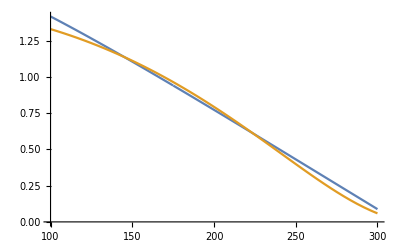

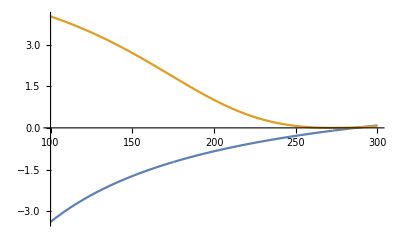

```mathematica
Plot[{Chop[N[PolyLog[2,X1[125,x,300]]]+N[PolyLog[2,X2[125,x,300]]]],
N[2*ArcTan[Y1[125,x,300]]^2]},{x,100,300}]
Plot[{Chop[N[PolyLog[2,X3[125,x,300]]]+N[PolyLog[2,X4[125,x,300]]]],
N[2*ArcTan[Y2[125,x,300]]^2]},{x,100,300}]
```

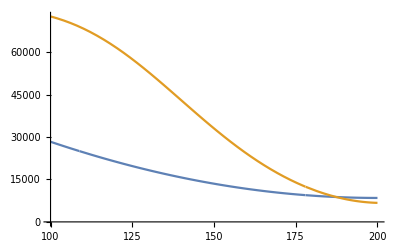

```mathematica
Plot[{200^2*Chop[N[PolyLog[2,X1[91.2,x,200]]]+N[PolyLog[2,X2[91.2,x,200]]]]+x^2Chop[N[PolyLog[2,X3[91.2,x,200]]]+N[PolyLog[2,X4[91.2,x,200]]]],
N[200^2*2*ArcTan[Y1[91.2,x,200]]^2]+x^2*2*ArcTan[Y2[91.2,x,200]]^2},{x,100,200}]
```

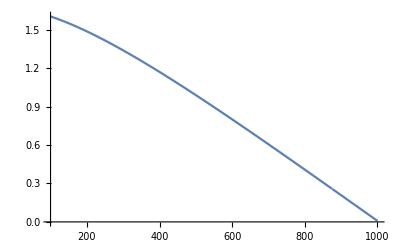

```mathematica
Plot[{Chop[N[PolyLog[2,X1[125,x,1000]]]+N[PolyLog[2,X2[125,x,1000]]]],
N[2*ArcTan[Y[125,x,1000]]^2]},{x,100,1000}]
```

```mathematica
ContourPlot[{Chop[N[PolyLog[2,X1[125,x,y]]]+N[PolyLog[2,X2[125,x,y]]]]-
N[2*ArcTan[Y[125,x,y]]^2]},{x,100,300},{y,100,300}]
```

-Graphics-

```mathematica
ContourPlot[{Chop[N[PolyLog[2,X1[91.2,x,y]]]+N[PolyLog[2,X2[91.2,x,y]]]]-
N[2ArcTan[Y[91.2,x,y]]^2]},{x,100,300},{y,100,300}]
```

-Graphics-

```mathematica
m2^2*(PolyLog[2,X1[mZ,m1,m2]]+PolyLog[2,X2[mZ,m1,m2]])+m1^2(PolyLog[2,X3[mZ,m1,m2]]+PolyLog[2,X4[mZ,m1,m2]])
```

m1^2 (PolyLog[2,(2 mZ^2)/(m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))]+PolyLog[2,(2 mZ^2)/(m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))])+m2^2 (PolyLog[2,(2 mZ^2)/(-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))]+PolyLog[2,(2 mZ^2)/(-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))])

```mathematica
Simplify[%]
```

m1^2 (PolyLog[2,(2 mZ^2)/(m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))]+PolyLog[2,(2 mZ^2)/(m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))])+m2^2 (PolyLog[2,(2 mZ^2)/(-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))]+PolyLog[2,(2 mZ^2)/(-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))])

```mathematica
FullSimplify[%]
```

m1^2 (PolyLog[2,(2 mZ^2)/(m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))]+PolyLog[2,(m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))/(2 m1^2)])+m2^2 (PolyLog[2,(2 mZ^2)/(-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))]+PolyLog[2,(-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))/(2 m2^2)])

```mathematica
PolyLog[2,0.5]
```

0.582241

```mathematica
Sum[(0.5^i/i^2),{i,1,100}]
```

0.582241

## Actual BSM Points Tests

Test point inputs: Higgs to diphoton & Zgamma
MSSM Folder #, Run #, stop mass 1, stop mass 2, mixing angle, c2ratio diphoton, c2ratio Zgamma

```mathematica
PLTS[s_,O_]:=Sum[(s^k/k^2),{k,O}]
```

### Point 1

General
1) 3160 177.813 183.958 -1.43528 0.0904086 0.0195464

```mathematica
Abs[X1[125,177.813,183.958]]
Abs[X2[125,177.813,183.958]]
Abs[X3[125,177.813,183.958]]
Abs[X4[125,177.813,183.958]]
```

0.679503

0.679503

0.702986

0.702986

```mathematica
PolyLog[2,X1[125,177.813,183.958]]
PLTS[X1[125,177.813,183.958],5]
```

0.156458+0.683129 ⅈ

0.155586+0.680351 ⅈ

```mathematica
PolyLog[2,X3[125,177.813,183.958]]
PLTS[X3[125,177.813,183.958],7]
```

0.0913416+0.707074 ⅈ

0.0916331+0.707966 ⅈ

### Point 2

General
2) 6927 147.197 262.658 -0.0587058 0.0900112 0.0445972

```mathematica
Abs[X1[125,147.197,262.658]]
Abs[X2[125,147.197,262.658]]
Abs[X3[125,147.197,262.658]]
Abs[X4[125,147.197,262.658]]
```

0.475904

0.475904

0.849202

0.849202

```mathematica
PolyLog[2,X1[125,147.197,262.658]]
PLTS[X1[125,147.197,262.658],5]
PolyLog[2,X3[125,147.197,262.658]]
PLTS[X3[125,147.197,262.658],7]
```

0.512681+0.179874 ⅈ

0.512832+0.179414 ⅈ

-0.650537+0.321273 ⅈ

-0.648927+0.319197 ⅈ

### Point 3

Close Masses
3) 950 190.033 191.091 1.16582 0.0809043 0.0159313

```mathematica
Abs[X1[125,190.033,191.091]]
Abs[X2[125,190.033,191.091]]
Abs[X3[125,190.033,191.091]]
Abs[X4[125,190.033,191.091]]
```

0.654139

0.654139

0.65778

0.65778

```mathematica
PolyLog[2,X1[125,190.033,191.091]]
PLTS[X1[125,190.033,191.091],5]
PolyLog[2,X3[125,190.033,191.091]]
PLTS[X3[125,190.033,191.091],7]
```

0.116993+0.658119 ⅈ

0.117016+0.655859 ⅈ

0.106305+0.661829 ⅈ

0.106578+0.662321 ⅈ

### Point 4

Distant Masses
4) 4432 136.812 421.425 0.0101265 0.0890884 0.0581019

```mathematica
Abs[X1[125,136.812,421.425]]
Abs[X2[125,136.812,421.425]]
Abs[X3[125,136.812,421.425]]
Abs[X4[125,136.812,421.425]]
```

0.882944

0.0996429

0.11067

7.54293

```mathematica
PolyLog[2,X1[125,136.812,421.425]]
PLTS[X1[125,136.812,421.425],5]
PolyLog[2,X4[125,136.812,421.425]]
PLTS[X4[125,136.812,421.425],7]
```

1.25721

1.21377

-3.55795

-24051.4

### Point 5

Big Mixing Angle
5) 9627 177.129 201.418 0.909586 0.082922 0.0223519

```mathematica
Abs[X1[125,177.129,201.418]]
Abs[X2[125,177.129,201.418]]
Abs[X3[125,177.129,201.418]]
Abs[X4[125,177.129,201.418]]
```

0.6206

0.6206

0.7057

0.7057

```mathematica
PolyLog[2,X1[125,177.129,201.418]]
PLTS[X1[125,177.129,201.418],5]
PolyLog[2,X3[125,177.129,201.418]]
PLTS[X3[125,177.129,201.418],15]
```

0.229+0.611526 ⅈ

0.22744+0.610625 ⅈ

-0.0187002+0.696486 ⅈ

-0.018698+0.696499 ⅈ